## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,NMinimize::cvmit,NIntegrate::slwcon];
```

### Various Constants

```mathematica
c=299792.458;
cH0=2997.92458;
Tcmb=2.7255;
```

#### Binned Pantheon Data

```mathematica
(* Import the Binned Pantheon Data *)
dataPanth=Import[".\\data\\lcparam_DS17f.txt","Table"];
ndatPanth=Length[dataPanth]-1;
(* Systematic Uncertainties *)
Dij0=Import[".\\data\\sys_DS17f.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
Covsys=Dij;
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

### LMT Model

```mathematica
(* Equivalent form of the LwMT Dark Energy Model as a function of α - See arxiv: 2012.13932 *)
w[a_,w0_,wa_,at_]:=w0+wa HeavisideTheta[1/a -1 /at]
(* Subscript[f, DE](α) for LwMT Dark Energy Model *)
f[a_,w0_,wa_,at_]:=ⅇ^(-3 ((1+w0) Log[a]+wa HeavisideTheta[1/a-1/at] Log[a/at]));
(* See Eq. (2) of arxiv:9709112 *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f[a,w0,wa,at]]
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=(DLsol[om,w0,wa,h,at]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,h,at]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,w0,wa,h,at])[[1]]//Chop
```

```mathematica
(* LMT values from MontePython *)
omlmt=0.302;
w0lmt=-1;
walmt=0;
ztlmt=0.01;
h0lmt=0.6836;
```

### PEDE Model

```mathematica
(* PEDE Dark Energy Model as a function of α *)
wPEDE[a_]:=-1/(3Log[10])(1+Tanh[Log10[1/a]])-1
(* Subscript[f, DE](α) for PEDE Dark Energy Model *)
fPEDE[a_]:=a^(1/Log[10])Sech[Log[a]/Log[10]];
HPEDE[a_?NumberQ,om_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))fPEDE[a]]
Clear[DLsolPEDE,DLPEDE,dLPEDE]
DLsolPEDE[om_?NumberQ,h_?NumberQ]:=(DLsolPEDE[om,h]=NDSolve[{D[dLPEDE[zz]/(1+zz),zz]==1/(HPEDE[1/(1+zz),om,h]/(100h)),dLPEDE[0]==0},dLPEDE,{zz,0,1300},MaxSteps->Infinity])
DLPEDE[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=(c/(100h)dLPEDE[z]/.DLsolPEDE[om,h])[[1]]//Chop
```

### CPL Model

```mathematica
(* nCPL Dark Energy Model as a function of α *)
wcpl[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
(* Subscript[f, DE](α) for nCPL Dark Energy Model *)
fcpl[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
Hcpl[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))fcpl[a,w0,wa,n]]
Clear[DLsolcpl,DLcpl,dLcpl]
DLsolcpl[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsolcpl[om,w0,wa,n,h]=NDSolve[{D[dLcpl[zz]/(1+zz),zz]==1/(Hcpl[1/(1+zz),om,w0,wa,n,h]/(100h)),dLcpl[0]==0},dLcpl,{zz,0,1300},MaxSteps->Infinity])
DLcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100h)dLcpl[z]/.DLsolcpl[om,w0,wa,n,h])[[1]]//Chop
```

```mathematica
(* Absolute Magnitude Plot for LMT *)
errall=Sqrt[Diagonal[Cijtot]];
listzt001=Table[{dataPanth[[1+i,2]],dataPanth[[1+i,5]]-Around[(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],omlmt,w0lmt,walmt,h0lmt,1/(1+ztlmt)]]+25),errall[[i]]]},{i,1,ndatPanth}];
(* Absolute Magnitude Plot for PEDE *)
listPEDE=={};
listPEDE=Table[{dataPanth[[1+i,2]],dataPanth[[1+i,5]]-Around[(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DLPEDE[dataPanth[[1+i,2]],0.281,0.7169]]+25),errall[[i]]]},{i,1,ndatPanth}];
(* Absolute Magnitude Plot for CPL*)
listCPL=={};
listCPL=Table[{dataPanth[[1+i,2]],dataPanth[[1+i,5]]-Around[(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DLcpl[dataPanth[[1+i,2]],0.295,-0.957,-0.38,1,0.695]]+25),errall[[i]]]},{i,1,ndatPanth}];
(* Absolute Magnitude Plot for wCDM*)
listWCDM=={};
listWCDM=Table[{dataPanth[[1+i,2]],dataPanth[[1+i,5]]-Around[(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DLcpl[dataPanth[[1+i,2]],0.2967,-1.038,0,1,0.6917]]+25),errall[[i]]]},{i,1,ndatPanth}];
```

```mathematica
hs[x_,k_]:=1/(1+Exp[-2k x])
mbf[mb1_,mb2_,x_,k_]:=mb1+(mb2-mb1) hs[x,k]
```

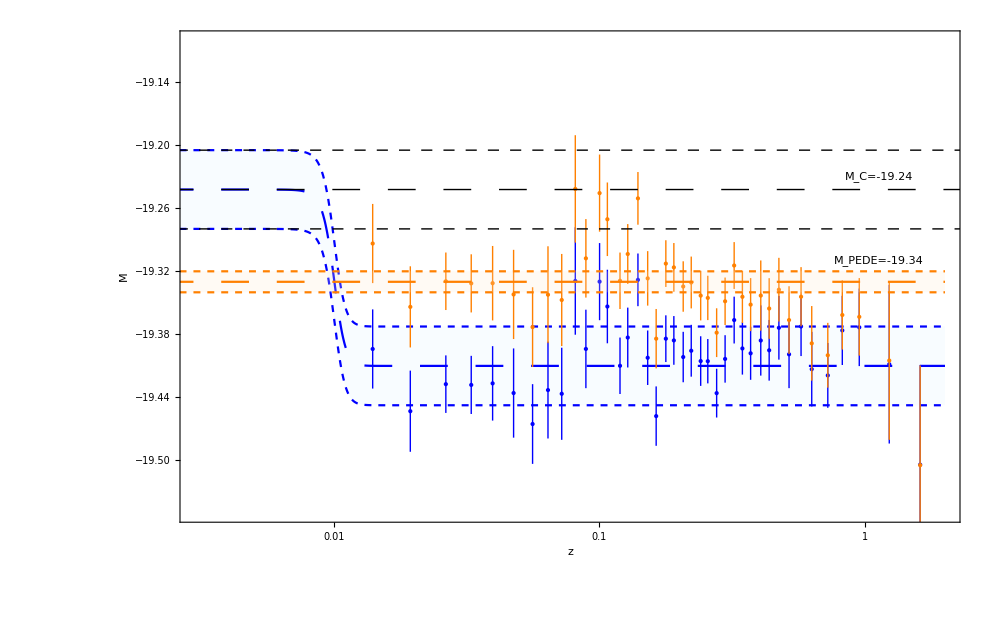

```mathematica
Mprior=−19.2421;
σMprior=0.0375;
pllmpt=ListLogLinearPlot[{listzt001}, Frame->True,FrameLabel->{"z","M"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Blue},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Prolog->{Inset[Framed[Column[{PointLegend[{Blue,Thickness[0.001],Dotted},{"LMT (z_t=0.01)"}]}],RoundingRadius->9],
Scaled[{0.88,0.9}]],Inset[Framed[Column[{PointLegend[{Orange,Thickness[0.001],Dotted},{"PEDE"}]}],RoundingRadius->9],
Scaled[{0.58,0.9}]]},Epilog->{Text["M_C=-19.24",{0.12,-19.23}],{Dashing[0.02],Line[{{-15,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-15,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-15,Mprior+σMprior},{8,Mprior+σMprior}}]}}, PlotRange->{{0,2},{-19.65,-19.1}}];
plPEDE=ListLogLinearPlot[{listPEDE}, Frame->True,FrameLabel->{"z","M"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Orange},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Prolog->{Inset[Framed[Column[{PointLegend[{Blue,Thickness[0.001],Dotted},{"LwMT (z_t=0.01)"}]}],RoundingRadius->9],
Scaled[{0.88,0.9}]],Inset[Framed[Column[{PointLegend[{Orange,Thickness[0.001],Dotted},{"PEDE"}]}],RoundingRadius->9],
Scaled[{0.58,0.9}]]},Epilog->{Text["M_C=-19.24",{0.12,-19.23}],{Dashing[0.02],Line[{{-15,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-15,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-15,Mprior+σMprior},{8,Mprior+σMprior}}]}}, PlotRange->{{0,2},{-19.65,-19.1}}];
Mprioru=Mprior+σMprior;
Mpriorbf=Mprior;
Mpriord=Mprior-σMprior;
dm=0.168;
zt=0.01;
dz=1/1000;
zmin=0.0005;
zmax=2;
plm=LogLinearPlot[{{mbf[Mprioru,Mprioru-dm,(z-zt),1/dz]},{mbf[Mpriorbf,Mpriorbf-dm,(z-zt),1/dz]},{mbf[Mpriord,Mpriord-dm,(z-zt),1/dz]}},{z,zmin,zmax}, Frame->True,Filling->{3->{1}},FillingStyle->{LightBlue,Opacity[0.7]},ImageSize->1000, FrameStyle -> Directive[Black, Thick],FrameLabel->{"z","M"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{{Dashed,Blue},{Dashing[0.02],Blue},{Dashed,Blue}}, PlotRange->{{0.003,2},{-19.55,-19.1}},Prolog->{Inset[Framed[Column[{PointLegend[{Blue,Thickness[0.001],Dotted},{"LMT (z_t=0.01)"}]}],RoundingRadius->9],
Scaled[{0.88,0.9}]],Inset[Framed[Column[{PointLegend[{Orange,Thickness[0.001],Dotted},{"PEDE"}]}],RoundingRadius->9],
Scaled[{0.71,0.9}]]},Epilog->{Text["M_PEDE=-19.34",{0.12,-19.31}],Text["M_C=-19.24",{0.12,-19.23}],{Dashing[0.02],Line[{{-15,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-15,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-15,Mprior+σMprior},{8,Mprior+σMprior}}]}}];
plmPEDE=LogLinearPlot[{-19.32,-19.33,-19.34},{z,zmin,zmax},PlotStyle->{{Dashed,Orange},{Dashing[0.02],Orange},{Dashed,Orange}},Filling->{3->{1}},FillingStyle->{LightOrange,Opacity[0.7]}];
Mbplot1=Show[plm,pllmpt,plPEDE,plmPEDE]
```

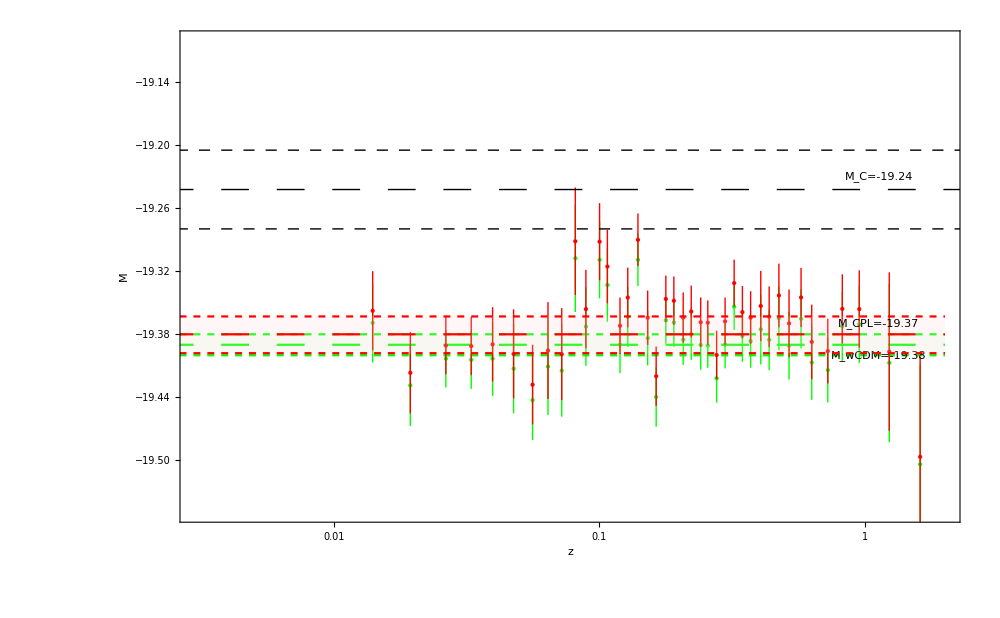

```mathematica
plwcdm1=ListLogLinearPlot[{listWCDM}, Frame->True,FrameLabel->{"z","M"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Green},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Prolog->{Inset[Framed[Column[{PointLegend[{Blue,Thickness
[0.001],Dotted},{"LwMPT (z_t=0.01)"}]}],RoundingRadius->9],
Scaled[{0.88,0.9}]],Inset[Framed[Column[{PointLegend[{Orange,Thickness[0.001],Dotted},{"PEDE"}]}],RoundingRadius->9],
Scaled[{0.58,0.9}]]},Epilog->{Text["M_C=-19.24",{0.12,-19.23}],{Dashing[0.02],Line[{{-15,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-15,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-15,Mprior+σMprior},{8,Mprior+σMprior}}]}}, PlotRange->{{0,2},{-19.65,-19.1}}];
plCPL=ListLogLinearPlot[{listCPL}, Frame->True,FrameLabel->{"z","M"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{{PointSize->Large,Red},{PointSize->Large,Red},{PointSize->Large,RGBColor[0,0.32,0]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Prolog->{Inset[Framed[Column[{PointLegend[{Red,Thickness[0.001],Dotted},{"CPL (w_0=-1, w_a=-0.19)"}]}],RoundingRadius->9],
Scaled[{0.82,0.9}]],Inset[Framed[Column[{PointLegend[{Red,Thickness[0.001],Dotted},{"PEDE"}]}],RoundingRadius->9],
Scaled[{0.55,0.9}]]},Epilog->{Text["M_C=-19.38",{0.12,-19.37}],{Dashing[0.02],Line[{{-15,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-15,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-15,Mprior+σMprior},{8,Mprior+σMprior}}]}}, PlotRange->{{0,2},{-19.65,-19.1}}];
Mprioru=Mprior+σMprior;
Mpriorbf=Mprior;
Mpriord=Mprior-σMprior;
dm=0.168;
zt=0.01;
dz=1/1000;
zmin=0.0005;
zmax=2;
plwcdm2=LogLinearPlot[{-19.39+0.01,-19.39,-19.39-0.01},{z,zmin,zmax}, Frame->True,Filling->{3->{1}},FillingStyle->{LightGreen,Opacity[0.7]},ImageSize->1000, FrameStyle -> Directive[Black, Thick],FrameLabel->{"z","M"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{{Dashed,Green},{Dashing[0.02],Green},{Dashed,Green}}, PlotRange->{{0.003,2},{-19.55,-19.1}},Prolog->{Inset[Framed[Column[{PointLegend[{Red,Thickness[0.001],Dotted},{"CPL (w_0=-0.957, w_a=-0.4)"}]}],RoundingRadius->9],
Scaled[{0.835,0.9}]],Inset[Framed[Column[{PointLegend[{Green,Thickness[0.001],Dotted},{"wCDM (w=-1.03)"}]}],RoundingRadius->9],
Scaled[{0.57,0.9}]]},Epilog->{Text["M_wCDM=-19.38",{0.12,-19.4}],Text["M_CPL=-19.37",{0.12,-19.37}],Text["M_C=-19.24",{0.12,-19.23}],{Dashing[0.02],Line[{{-15,Mprior},{8,Mprior}}]},{Dashing[0.008],Line[{{-15,Mprior-σMprior},{8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{-15,Mprior+σMprior},{8,Mprior+σMprior}}]}}];
plmCPL=LogLinearPlot[{-19.38+0.017,-19.38,-19.38-0.018},{z,zmin,zmax},PlotStyle->{{Dashed,Red},{Dashing[0.02],Red},{Dashed,Red}},Filling->{3->{1}},FillingStyle->{LightRed,Opacity[0.7]}];
Mbplot2=Show[plwcdm2,plwcdm1,plCPL,plmCPL]
```

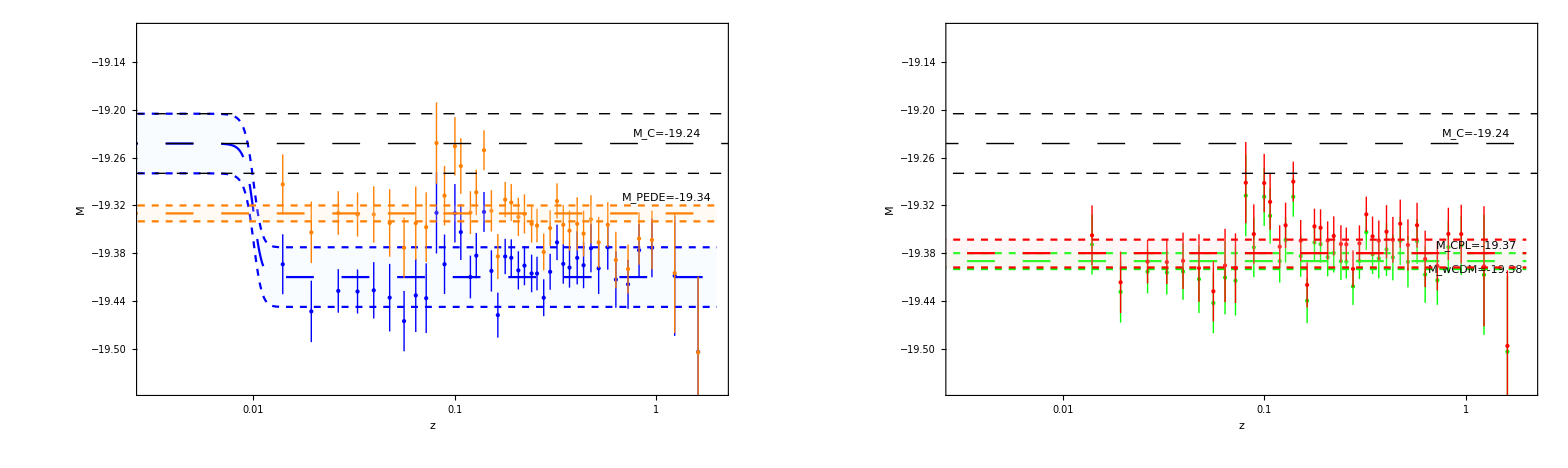

```mathematica
Mbplot=GraphicsGrid[{{Mbplot1,Mbplot2}},ImageSize->2000]
```

```mathematica
Export[NotebookDirectory[]<>"mzplt.pdf",Mbplot,ImageResolution->1000];
```